ListPlot::sclfn: The scaling function {Reverse,Log10} cannot be used to scale coordinates.

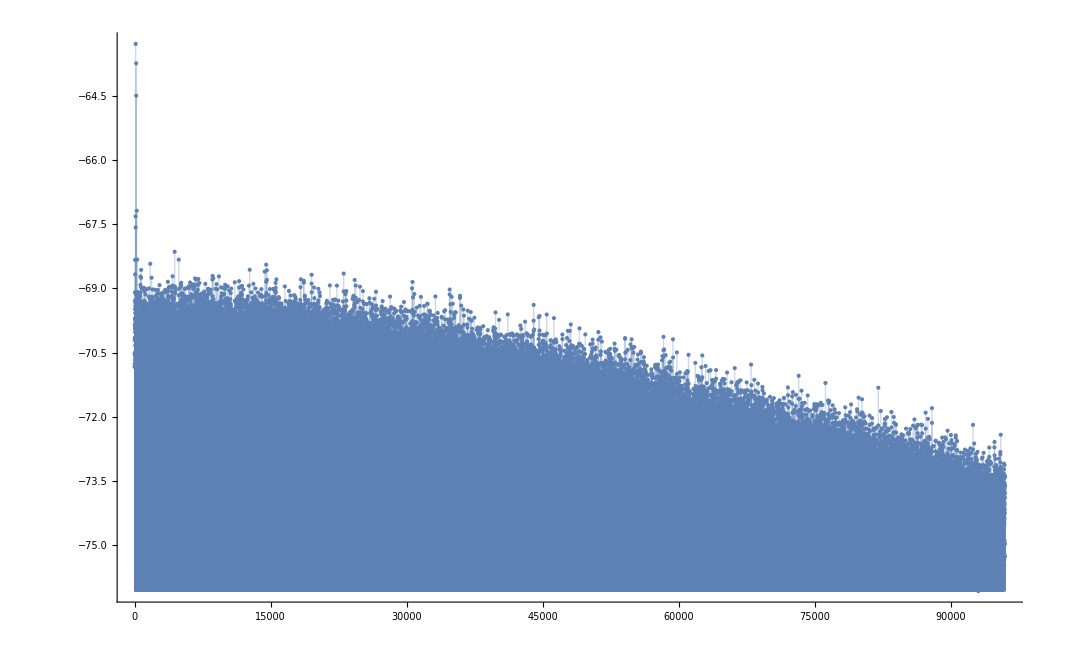

```mathematica
dtset2 = Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/10_Lab/10_data/2-part/1k_bot_inverse.txt", "TSV"];
TableForm[dtset2];
col1 = dtset2[[All, 1]][[2 ;; 32768]]; (*Frequency*)
col2 = dtset2[[All, 2]][[2 ;; 32768]]; (*Noise*)

dtIp2 = {col1, col2};
dB2 = Transpose[dtIp2];

ListPlot[dB2, ScalingFunctions->{"Reverse", Log10}, Filling->Bottom]
```